```mathematica
fullSimplifyReal[x_]:=Assuming[_Symbol ∈ Reals , FullSimplify@x]


CL=2.997925 10^10;
Gr=6.67 10^-8;
ARAD=7.56464 10^(-15);
KPE=0.4;
SGT=6.6524 10^-25; (*Thomson cross section cm^2*)
RGAS=8.31 10^7;
KB=1.38062 10^-16;
PC=3.085678 10^18;
Msol=1.989 10^33;
MBH=10^7 * Msol;
MP=1.672661 10^-24;
SGB = ARAD*CL/4;
DAY = 24 3600;
YR=31536000;
MsolYr = Msol/YR;

MdotNumber[M_]:= η ϵ^-1 4Pi CL Gr M/KPE/CL^2
SchwarzchildRadius[M_]:=2Gr M /CL^2;
```

```mathematica
0.01PC
15PC
SchwarzchildRadius[MBH]
0.01PC/SchwarzchildRadius[MBH]
15PC/SchwarzchildRadius[MBH]
```

3.08568×10^16

4.62852×10^19

2.95222×10^12

10452.1

1.56781×10^7

Accretion scales

```mathematica
Eddington accretion rate:
```

```mathematica
Integrate[Sqrt[1+Sqrt[x]],x]
```

4/15 (1+√x)^(3/2) (-2+3 √x)

```mathematica
Module[{ri,  MBH=10^7 Msol Subscript[M, 7]},
ri=3*2Gr MBH/CL^2;

Print["Mdot_edd = ", 4Pi CL ri /KPE/MsolYr ," MsolYr"]
]
```

Mdot_edd = 0.132255 M_7 MsolYr

Thin disk aspect ratio:

```mathematica
OmegaOrb[r_,M_]:=√(Gr M) r^(-3/2)

VelocOrb[r_,M_]:=√(Gr M) r^(-1/2)
```

```mathematica
ClearAll[r ]

Tdisk = TempDisk[0.5PC,0.01MsolYr,MBH]
Vtherm[T_]:= Module[{μ=1},(RGAS/μ T)^(1/2)]


Print["Thin disk at R_0.5: H/R = ", Vtherm[T]/VelocOrb[0.5 Subscript[r, 0.5] PC,10^7 Msol Subscript[M, 7]]/.T->Tdisk ]


Print["Thin disk at R_AGN: H/R = ", Vtherm[50 Subscript[T, 50]]/VelocOrb[Subscript[r, 1] PC,10^7 Msol Subscript[M, 7]] ]

ClearAll[Tdisk]
```

TempDisk[1.54284×10^18,6.30708×10^23,1.989×10^40]

Thin disk at R_0.5: H/R = (0.000310871 √(r_0.5) √TempDisk[1.54284×10^18,6.30708×10^23,1.989×10^40])/(√M_7)

Thin disk at R_AGN: H/R = (0.00310871 √r_1 √T_50)/(√M_7)

```mathematica
Module[{RBHSphInfluence, MBH=10^7 Msol Subscript[M, 7] ,res},
RBHSphInfluence = (Gr MBH)/((100 10^5 Subscript[σ, 100])^2);
res=Vtherm[50 Subscript[T, 50]]/VelocOrb[RBHSphInfluence,MBH]//FullSimplify;
Print["Thin disk: H/R(r_BHS) = ",  res]
]
```

Thin disk: H/R(r_BHS) = (0.00644593 √T_50 √(M_7/σ_100^2))/(√M_7)

Sublimation outer, radius outer:

```mathematica
RadSub[L_]:=Module[{Ts=1500, ϵ=ϵ01, Mdt = 0.1Msolyr},

	(L/(4Pi SGB Ts^4))^(1/2)]

Print[" Sublimation radius:\n ", "R_s = ",
RadSub[Subscript[f, c] 4Pi Gr CL MBH/KPE]/PC/.Subscript[f, c]->0.5 Subscript[f, 0.1], "pc"]
```

Sublimation radius:\n R_s = 0.134877 √(f_0.1)pc

Sublimation Inner radius, disk :

(0.132255 M_7 η_0.5)/(ϵ_0.1)

```mathematica
(* solving for inner Subscript[r, in] *)
Solve[((3/π)^(1/4) ((G M Ṁ)/(r^3 σ))^(1/4))/2^(3/4) == Subscript[T, s],r]
```

{{r→-(G^(1/3) M^(1/3) (-3/π)^(1/3) (Ṁ)^(1/3))/(2 σ^(1/3) T_s^(4/3))},{r→(G^(1/3) M^(1/3) (3/π)^(1/3) (Ṁ)^(1/3))/(2 σ^(1/3) T_s^(4/3))},{r→((-1)^(2/3) G^(1/3) M^(1/3) (3/π)^(1/3) (Ṁ)^(1/3))/(2 σ^(1/3) T_s^(4/3))}}

Disk temperature :

```mathematica
TempDisk [r_, Mdot_,M_]:=(3/(8 π)(G M)/r^3 Mdot/σ)^(1/4)
(*Solve[((3/π)^(1/4) ((G M Ṁ)/(r^3 σ))^(1/4))/2^(3/4) == Subscript[T, s],r]*)
rFunOfT= Assuming[{r>0 && Ṁ>0 && M>0 && G>0 && σ>0 && T>0 && π>0},
	Solve[TempDisk[r, Mdot, M] == T, r]
]⟦2⟧
```

{r→(G^(1/3) M^(1/3) Mdot^(1/3) (3/π)^(1/3))/(2 T^(4/3) σ^(1/3))}

The escape velocity of at r(T) U_sc=((G M)/r)^(1/2)

```mathematica
rIronBump=fullSimplifyReal[((G M)/r)^(1/2)/.rFunOfT]/.{π->Pi,G->Gr,σ->SGB,T->1.8 10^5, M->MBH,Mdot->0.1MsolYr}
rIronBump/10^5
```

7.1985×10^9

71985.

```mathematica
ClearAll[M]
ClearAll[ϵ,η]

MdotNumber[M_]:= η ϵ^-1 4Pi CL Gr M/KPE/CL^2

MdotNumber[MBH Subscript[M, 7]]/MsolYr/.{ϵ->0.1 Subscript[ϵ, 0.1], η->0.6 Subscript[η, 0.5]}

SchwRad[M_]:= 2Gr M/CL^2

RSubInner[M_, Mdot_]:=(G^(1/3) M^(1/3) (3/π)^(1/3) Mdot^(1/3))/(2 σ^(1/3) Subscript[T, s]^(4/3))
Print@"Mdot(g s^-1)="
Md1 =MdotNumber[MBH Subscript[M, 7]]/.{ϵ->0.1 Subscript[ϵ, 0.1], η->0.6 Subscript[η, 0.5]}

res = RSubInner[MBH Subscript[M, 7], Md1]/.{G->Gr, σ->SGB, Subscript[T, s]-> 1500 } ;

Print@"(* inner sublimation radius in various units *)"
 
 Rin = Assuming[Subscript[M, 7]>0, Simplify[res]]
res=Rin;

Print@"(*       in parsecs:       *)"
res/PC "pc"

Print@"(*       in R_g:            *)"
res/SchwRad[MBH]"rg"

Print@"(*     Local  radiation flux ergs:      *)"

FluxDisk[r_, Mdot_,M_] := 3/(8Pi)(Gr M)/r^3 Mdot;

FluxDisk[Rin, Md1,MBH]



Print@"(*     External  radiation flux ergs:   *)"
FluxExtern[r_, η_,M_]:=η CL Gr MBH/KPE/r^2;
FluxExtern[Rin, 0.5 Subscript[η, 0.5], MBH]
```

(0.132255 M_7 η_0.5)/(ϵ_0.1)

Mdot(g s^-1)=

(8.34144×10^24 M_7 η_0.5)/(ϵ_0.1)

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of T_50.

(* inner sublimation radius in various units *)

res

(*       in parsecs:       *)

3.24078×10^-19 pc res

(*       in R_g:            *)

3.38728×10^-13 rg res

(*     Local  radiation flux ergs:      *)

(1.32094×10^57 M_7 η_0.5)/(res^3 ϵ_0.1)

(*     External  radiation flux ergs:   *)

(4.97155×10^43 η_0.5)/res^2

```mathematica
Solve[((3/π)^(1/4) ((G M Ṁ)/(r^3 σ))^(1/4))/2^(3/4)==Subscript[T, s],r]
```

```mathematica
Print@"(* solving for inner r_out *)"

RSubOuter[M_]:=(η 4Pi CL Gr M/KPE/4/Pi/SGB/Subscript[T, s]^4)^(1/2)

Rout =RSubOuter[MBH Subscript[M, 7]]/.{ϵ->0.1 Subscript[ϵ, 0.1], η->0.5 Subscript[η, 0.5],Subscript[T, s]-> 1500 }
Rin
Assuming[Subscript[M, 7]>0 && Subscript[η, 0.5]>0 && Subscript[ϵ, 0.1]>0,
Simplify[Rout/Rin]
]
(*Rout/PC "pc"*)

Print@"external flux equals local flux at"

ClearAll[η]
3/(8Pi)KPE/(CL η)MdotNumber[MBH Subscript[M, 7]]/.ϵ->0.1 Subscript[ϵ, 0.1]
%/PC

%%/Rin
Rout
Print@"Escape velocity at Rin:"
√(Gr MBH/Rin)/10^5

Print@"Escape velocity at Rout:"
√(Gr MBH/Rout)/10^5
```

(* solving for inner r_out *)

4.16187×10^17 √(M_7 η_0.5)

1.66337×10^16 ((M_7^2 η_0.5)/(ϵ_0.1))^(1/3)

25.0207 ϵ_0.1^(1/3) ((η_0.5)/M_7)^(1/6)

external flux equals local flux at

(2.21417×10^13 M_7)/(ϵ_0.1)

(7.17563×10^-6 M_7)/(ϵ_0.1)

(0.00133113 M_7)/(ϵ_0.1 ((M_7^2 η_0.5)/(ϵ_0.1))^(1/3))

4.16187×10^17 √(M_7 η_0.5)

Escape velocity at Rin:

2824.14/(((M_7^2 η_0.5)/(ϵ_0.1))^(1/6))

Escape velocity at Rout:

564.594/(M_7 η_0.5)^(1/4)

```mathematica
(*/MsolYr/.{ϵ->0.1 Subscript[ϵ, 0.1], η->0.6 Subscript[η, 0.5]}*)
```

external flux equals local flux at

(2.21417×10^12 M_7)/ϵ

(7.17563×10^-7 M_7)/ϵ

(0.000133113 M_7)/(ϵ ((M_7^2 η_0.5)/(ϵ_0.1))^(1/3))

Rout

Escape velocity at Rin:

2824.14/(((M_7^2 η_0.5)/(ϵ_0.1))^(1/6))

```mathematica
Rsch[M_]:= 2Gr M/CL^2;

OpacFreeFree[n_,T_]:= 0.11 T^(-7/2)n

OpacFreeFree[10^11,10^3]
```

0.347851

α-disk solution:

Basic equations :

```mathematica
ClearAll[Eq1,Eq2,Eq3,Eq4,Eq5,Eq6,Eq7,T,α]

OmegaOrb[r_,M_]:=√(G M) r^(-3/2)

VelocOrb[r_,M_]:=√(G M) r^(-1/2)

EqHoriz = Σ ν -Mdt/(3π)J
EqVertTtau = T^4-3/4 τ0 T04  (* T04 = Subscript[T, 0]^4 *)

EqTempViscDissp =  T04 - 9/(8σ)Ω^2 ν Σ

EqNu = ν-> α C^2/Ω

EqVertHeight=H0-> C/Ω

EqC2= C^2-> Rg T/m

EqTau=τ0->1/2 κ Σ

EqSigmaHRho =Σ->2H ρ

OmegaOrbAn[r_,M_]:=√(G M) r^(-3/2)

EqC = EqVertHeight/.C->√EqC2[[2]]

(*get rid of T0*)


EqNu = EqNu/.EqC2;
EqHoriz0= EqHoriz/.EqNu

EqVertTtau0 = EqVertTtau/.EqTau/.Solve[EqTempViscDissp==0, T04]/.EqNu
%//Last
```

-(J Mdt)/(3 π)+ν Σ

T^4-(3 T04 τ0)/4

T04-(9 ν Σ Ω^2)/(8 σ)

ν→(C^2 α)/Ω

H0→C/Ω

C^2→(Rg T)/m

τ0→(κ Σ)/2

Σ→2 H ρ

H0→(√((Rg T)/m))/Ω

-(J Mdt)/(3 π)+(Rg T α Σ)/(m Ω)

{T^4-(27 Rg T α κ Σ^2 Ω)/(64 m σ)}

T^4-(27 Rg T α κ Σ^2 Ω)/(64 m σ)

```mathematica
EqHoriz0
EqVertTtau0

EqSigma0 = EqVertTtau0/.Solve[ EqHoriz0==0, T]

Assuming[ T>0 && Rg>0 && α>0 && κ>0 && Σ>0 && Ω>0 && m>0 && σ>0 && J>0 && Mdt>0 && π>0,
	EqSigma0 = Solve[ EqSigma0==0 , Σ][[2]]
]
EqSigma0=Assuming[M>0&&r>0,
Simplify[
	EqSigma0/.Ω->OmegaOrb[r,M]/.{Rg->RGAS, σ->SGB, m->1, κ->KPE}//N
]
] 

Msc = Msol;
Rsc = 3 Rsch[Msc];
Mdotsc = 3 10^-8 MsolYr;

"Substitute numbers into EqSigma0 ="
EqSigma0/.{r->Rsc r, M->Msc m, Mdt->Mdotsc mdt}


(*----------------------------------------------------------------------------------------*)
"EqT1 = "
EqT1 = EqVertTtau0/.Solve[ EqHoriz0==0, Σ]

"ADiskTemp="
ADiskTemp=Assuming[M>0&&r>0,
	Simplify[
		Solve[EqT1==0,T][[2]]/.Ω->OmegaOrbAn[r,M]
	]
]

(*ADiskTempKPE= ADiskTemp/.{m->1, κ->KPE}
ADiskTempScaled=ADiskTempKPE/.{r->Rsc r, M->Msc m, Mdt->Mdotsc mdt}
*)

(*----------------------------------------------------------------------------------------*)
```

-(J Mdt)/(3 π)+(Rg T α Σ)/(m Ω)

{T^4-(27 Rg T α κ Σ^2 Ω)/(64 m σ)}

{{-(9 J Mdt κ Σ Ω^2)/(64 π σ)+(J^4 m^4 Mdt^4 Ω^4)/(81 π^4 Rg^4 α^4 Σ^4)}}

{Σ→(2 (2/3)^(1/5) J^(3/5) m^(4/5) Mdt^(3/5) σ^(1/5) Ω^(2/5))/(3 π^(3/5) Rg^(4/5) α^(4/5) κ^(1/5))}

{Σ→(2.42671×10^-8 J^(3/5) (G M)^(1/5) (Mdt/r)^(3/5))/α^(4/5)}

Substitute numbers into EqSigma0 =

{Σ→(2.77046×10^6 J^(3/5) (G m)^(1/5) (mdt/r)^(3/5))/α^(4/5)}

EqT1 =

{{T^4-(3 J^2 m Mdt^2 κ Ω^3)/(64 π^2 Rg T α σ)}}

ADiskTemp=

{T→((3/2)^(1/5) J^(2/5) m^(1/5) (G M)^(3/10) Mdt^(2/5) κ^(1/5))/(2 π^(2/5) r^(9/10) Rg^(1/5) α^(1/5) σ^(1/5))}

Temperature T_eff is significantly smaller than T_c.

```mathematica
EqHoriz
EqVertTtau
EqTempViscDissp
```

-(J Mdt)/(3 π)+ν Σ

T^4 σ-(3 T04 τ0)/4

T04 σ-9/8 ν Σ Ω^2

(1.39024×10^24 η)/ϵ

((3/2)^(1/5) J^(2/5) m^(1/5) (G M)^(3/10) Mdt^(2/5) κ^(1/5))/(2 π^(2/5) r^(9/10) Rg^(1/5) α^(1/5) σ^(1/5))

6.77381 ((G J M Mdt)/r^3)^(1/4)

Teff =

19.067

TcFun  =

(3.93335×10^18)/r^(9/10)

Rin =

9.15389×10^15

1.86125×10^17

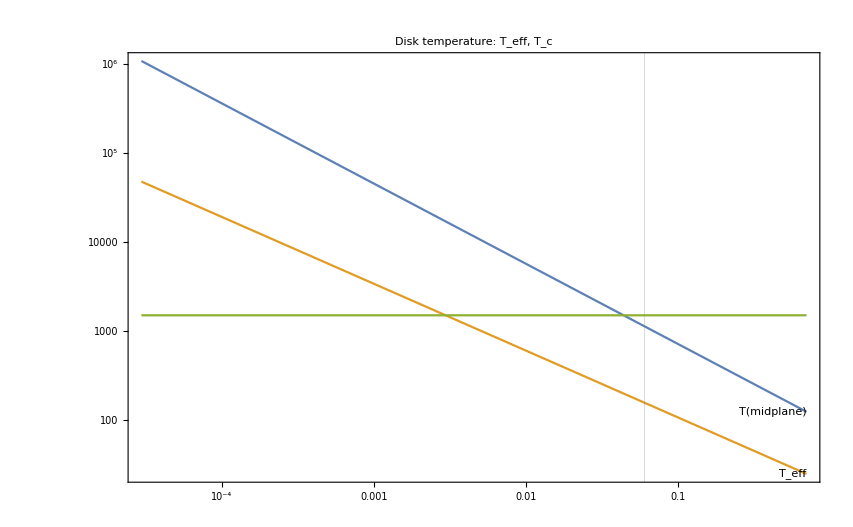

```mathematica
ClearAll[AdiskTempSufaceFunc,ADiskTempFunc,J, Mdt,TcFun,ADiskTempFunc]

Msc = MBH;
Rsc = 1PC;
(*Mdotsc = 3 10^-8 MsolYr;*)
Mdotsc= MdotNumber[MBH]

(*midplane temperature*)

ADiskTempFunc[r_, M_, Mdt_] = fullSimplifyReal[ADiskTemp[[1]][[2]]]


AdiskTempSufaceFunc[r_, M_, Mdt_]=
	(Part[ Solve[EqTempViscDissp==0, T04]/.Solve[EqHoriz==0, ν]/.Ω->OmegaOrb[r,M]/.{σ->SGB}//Flatten, 1,2])^(1/4)


"Teff ="
TeffFun[r_]:=Block[{J=1, ϵ=0.1, η=0.1},
	AdiskTempSufaceFunc[r, Msc, Mdotsc]/.{J->1, m->1,Rg->RGAS, σ->SGB,G->Gr}
	]
TeffFun[Rsc]	

TcFun[r_]:=Block[{α=0.5, ϵ=0.1, η=0.1, κ=5},
	ADiskTempFunc[r, Msc, Mdotsc]/.{J->1, m->1,Rg->RGAS, σ->SGB,G->Gr}
]

"TcFun  ="
TcFun[r]
RSubInnerNumber[M_, Mdot_,Ts_]:=(G^(1/3) M^(1/3) (3/π)^(1/3) Mdot^(1/3))/(2 σ^(1/3) Ts^(4/3))/.{G->Gr,σ->SGB}

"Rin ="
Rin = Block[{α=0.5, ϵ=0.1, η=0.1, T=1500}, RSubInnerNumber[Msc, Mdotsc, T]]

(*        Temperature plot        *)
 
 RSubAGN = ((η Ledd)/(4 π σ Subscript[T, s]^4))^(1/2)/.Ledd->(4π c G M)/κ/.{G->Gr,σ->SGB,κ->KPE,c->CL, M->MBH}/.{α->0.5, ϵ->0.1, η->0.1, Subscript[T, s]->1500}
 
 
LogLogPlot[
  {TcFun[r PC],TeffFun[r PC], 1500}, {r, 0.01 Rin/PC, 0.7 Rsc/PC},
  GridLines -> {{{RSubAGN/PC,Thick}}, {}},
  (*PlotLegends->"Expressions",*)
  PlotLabel->"Disk temperature: T_eff, T_c",
  PlotLabels->Placed[{"T(midplane)","T_eff"},{Scaled[1],Left}],
  Frame->True
	]
	
(*Module[{xmin=0.1,xmax=10,ymin=0.1,ymax=1,dt=0.4,X1,Y1,f1,f2,fy},
f1[x_]:=x^4;
f2[x_]:=Sin[x];


X1 = Range[xmin,xmax,dt];
Y1 = Range[ymin,ymax,dt];

fy= MapThread[{#1,#2}&,{X1,f1 /@ X1}];

ListLogLogPlot[fy,Joined->True]
]*)
```

```mathematica
VelocOrb[0.001PC,MBH]/10^5
ARAD 1000^4/3
3/(8Pi)//N
```

6557.

0.00252155

0.119366

```mathematica
(*simpADiskTempFunc = fullSimplifyReal[ADiskTempFunc[r, M, Mdt]]*)

Print["T_c = ",  
	Tc = Block[{J=1, ϵ=0.1, η=0.1, Mdotsc=0.1 MsolYr Subscript[Mt, 0.1]},
		ADiskTempFunc[r, MBH Subscript[M, 7], Mdotsc] ]/.{J->1, m->1,Rg->RGAS, σ->SGB,G->Gr}		
		]
		
		
Assuming[{Ts>0,Subscript[M, 7]>0&&Subscript[Mt, 0.1]>0&&κ>0&&α>0&&Ts>0},
Solve[Tc==Ts, r, Reals]
]
ClearAll[Tc]
```

T_c = (4.5442×10^18 κ^(1/5) M_7^(3/10) Mt_0.1^(2/5))/(r^(9/10) α^(1/5))

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→ConditionalExpression[Root[Ts^10 α^2 #1^9-3.75472×10^186 κ^2 M_7^3 Mt_0.1^4&,1],M_7>0&&Mt_0.1>0&&κ>0&&α>0&&Ts>0]}}

Calculate R_do- two disk  sublimation radii:

```mathematica
(* ------------ the disk outer sublimation radius ---------------- *)
 
ClearAll[RoutdAn,RoutdA, RoutdNum,RoutdNum,α, ϵ, η]
ClearAll[res,Rout2,Rout2fun]

RoutdA = fullSimplifyReal@Solve[ADiskTempFunc[r, M, Mdt]==Ts,r]//Flatten
RoutdA = Part[RoutdA,1,2]


Rout2fun[M_] = RoutdA (*/.{G->Gr,Rg->RGAS, σ->SGB, m->1,J->1}//N*)

"Rout2="
Rout2fun[MBH]

myAssumptions1 = {Subscript[α, 0.1]>0 && Subscript[η, 0.1]>0 && Subscript[ϵ, 0.1]>0 && Subscript[M, 7]>0};


RoutdNum=RoutdA/.{G->Gr,Rg->RGAS, σ->SGB, m->1,J->1,
			Ts->1500,M->MBH Subscript[M, 7], κ->1, Mdt->Mdotsc}/.{α ->0.1 Subscript[α, 0.1], ϵ->0.1 Subscript[ϵ, 0.1], η->0.1 Subscript[η, 0.1]}


RoutdNum=Assuming[myAssumptions1,Simplify[RoutdNum]]

						
RoutdNum/PC			

(*"Routc ="
Routc = Block[{α=0.5, ϵ=0.1, η=0.1, T=1500}, RoutdNum[Msc, Mdotsc, T]]
*)
```

{r→3^(2/9)/(2 2^(1/3) π^(4/9) ((Rg^(1/5) Ts α^(1/5) σ^(1/5))/(J^(2/5) m^(1/5) (G M)^(3/10) Mdt^(2/5) κ^(1/5)))^(10/9))}

3^(2/9)/(2 2^(1/3) π^(4/9) ((Rg^(1/5) Ts α^(1/5) σ^(1/5))/(J^(2/5) m^(1/5) (G M)^(3/10) Mdt^(2/5) κ^(1/5)))^(10/9))

3^(2/9)/(2 2^(1/3) π^(4/9) ((Rg^(1/5) Ts α^(1/5) σ^(1/5))/(J^(2/5) m^(1/5) (G M)^(3/10) Mdt^(2/5) κ^(1/5)))^(10/9))

Rout2=

(8.25233×10^12)/(((Rg^(1/5) Ts α^(1/5) σ^(1/5))/(G^(3/10) J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5)))^(10/9))

(1.35474×10^17)/(((α_0.1^(1/5))/(M_7^(3/10) ((η_0.1)/(ϵ_0.1))^(2/5)))^(10/9))

(1.35474×10^17 M_7^(1/3))/(((α_0.1 ϵ_0.1^2)/(η_0.1^2))^(2/9))

(0.0439042 M_7^(1/3))/(((α_0.1 ϵ_0.1^2)/(η_0.1^2))^(2/9))

```mathematica
Clear[res]

Evaluate[RoutdA]

res[M_]=RoutdA

res[1]
```

3^(2/9)/(2 2^(1/3) π^(4/9) ((Rg^(1/5) Ts α^(1/5))/(J^(2/5) m^(1/5) (G M)^(3/10) κ^(1/5) (Mdt/σ)^(2/5)))^(10/9))

3^(2/9)/(2 2^(1/3) π^(4/9) ((Rg^(1/5) Ts α^(1/5))/(J^(2/5) m^(1/5) (G M)^(3/10) κ^(1/5) (Mdt/σ)^(2/5)))^(10/9))

3^(2/9)/(2 2^(1/3) π^(4/9) ((Rg^(1/5) Ts α^(1/5))/(G^(3/10) J^(2/5) m^(1/5) κ^(1/5) (Mdt/σ)^(2/5)))^(10/9))

```mathematica
3^(2/9)/(2 2^(1/3) π^(4/9) ((Rg^(1/5) Ts α^(1/5))/(J^(2/5) m^(1/5) (G M)^(3/10) κ^(1/5) (Mdt/σ)^(2/5)))^(10/9))
```

```mathematica
res ={1+√-9,1,{√-9}}
Attributes[res]
MemberQ[{1,2,2,12,,0,3,2},2]
MatchQ[#,_Complex] &/@ Flatten[res]
```

{1+3 ⅈ,1,{3 ⅈ}}

{}

True

{True,False,True}

```mathematica
(*density*)

ClearAll[res,res1,res2]
res1=Eq10/.EqSigmaHRho/.EqH0
res1=Solve[res1==0,T][[2]];

res2=Eq20/.EqSigmaHRho/.EqH0;
res2=Solve[res2==0,T][[4]];

res1=T/.res1;
res2=T/.res2;

res2= Numerator@Together[res1-res2];
ADiskRho = Assuming[m>0,
Simplify[
Solve[ res2==0,ρ][[1]]/.Ω->OmegaOrb[r,M]/.{Rg->RGAS, σ->SGB, κ->KPE}//N
]]

ADiskRhoScaled = ADiskRho/.{r->Rsc r, M->Msc, Mdt->Mdotsc mdt};
Assuming[{α>0,μ>0,M>0},
ADiskRhoScaled[[1]][[2]]/MP
]
```

ReplaceAll::reps: {EqH0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Eq10/.EqH0

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {EqH0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 4 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{}⟦4⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

Part::partw: Part 2 of {} does not exist.

5.9785×10^23 {}⟦2⟧

```mathematica
AdiskH0 = Assuming[m>0&&r>0&&Mdt>0 && J>0 && α>0,
	Simplify[EqSigma0[[1]][[2]]/2/ρ /.ADiskRho]
];

Print["H =", AdiskH0];
(*AdiskH0Scaled = AdiskH0/.{r->Rsc r, M->Msc M, Mdt->Mdotsc mdt}*)

AdiskH0OverR = AdiskH0/r/.{r-> 10^6 Subscript[r, 6], M->Msol Subscript[m, odot], Mdt-> 10^16 Subscript[mdt, 16]}
```

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

H =(1.21335×10^-8 (G M)^(1/5) ((J Mdt)/r)^(3/5))/(α^(4/5) ρ)/.{}⟦1⟧

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

((55426.1 (G m_odot)^(1/5) ((J mdt_16)/r_6)^(3/5))/(α^(4/5) ρ)/.{}⟦1⟧)/(1000000 r_6)

```mathematica
(*RSubInnerNumber[MBH Subscript[M, 7], MdotNumber[MBH Subscript[M, 7]]]/.{ϵ->0.1 Subscript[ϵ, 0.1], η->0.6 Subscript[η, 0.5]}*)
```

0.051978

```mathematica
MdotNumber[MBH]:= η ϵ^-1 4Pi CL Gr M/KPE/CL^2



SchwRad[M_]:= 2Gr M/CL^2

R
```

2.98925×10^48

```mathematica
Energy flux: from the disk:
```

```mathematica
ClearAll[M,Subscript[M, 7],r]
FluxDisk[r_, Mdot_,M_]:=3/(8Pi)(Gr M)/r^3 Mdot
FluxDisk==FluxDisk[0.1PC Subscript[r, 0.1],0.1 M01  MsolYr, 10^7 Subscript[M, 7] Msol]

(*Module[{M=10^7 Msol ,Fd, Fext, f=0.1f01},
Fd = FluxDisk[0.5PC Subscript[r, 0.5], 0.1 M01  MsolYr];
Fext = f
]*)

Solve[FluxDisk[r, Mdot,M]==
```

ClearAll::ssym: M_7 is not a symbol or a string.

FluxDisk==(33995.3 M01 M_7)/(r_0.1^3)

(7.96173×10^-9 M Mdot)/r^3

```mathematica
TempDisk [r_, Mdot_,M_]:=(3/(8Pi)(Gr M)/r^3 Mdot/SGB)^(1/4)

ClearAll[r]

TempDisk[1PC,0.01MsolYr,MBH]
```

15.6483

Temperature of the disk:

```mathematica
TempDisk [r_, Mdot_,M_]:=(FluxDisk[r, Mdot,M]/SGB)^(1/4);

TempDisk[1PC Subscript[r, 0.5],0.01M01  MsolYr,10^7 Subscript[M, 7] Msol]
```

15.6483 ((M01 M_7)/(r_0.5^3))^(1/4)

Disk aspect ratio without illumination :

```mathematica
Module[{Td},
Td=TempDisk[0.5PC Subscript[r, 0.5],0.1 M01  MsolYr,10^7 Subscript[M, 7] Msol];

Print["Thin disk at R_0.5: H/R = ", 
Simplify[
Vtherm[Td]/VelocOrb[0.5 Subscript[r, 0.5] PC,10^7 Msol Subscript[M, 7]] ,
Subscript[M, 7]>0 && M01>0 && Subscript[r, 0.5]>0

]
]]
```

Thin disk at R_0.5: H/R = 0.00212667 ((M01 r_0.5)/M_7^3)^(1/8)

```mathematica
ClearAll[M,r,FluxDiskExtern]
FluxDiskExtern[r_,M_]:=Module[{Fedd, H2R= 0.002 Subscript[ϵ, 0.002]},

Fedd = 4Pi CL Gr M/KPE/(4Pi r^2) H2R;

Fedd

]

FluxDiskExtern[0.5PC Subscript[r, 0.5],0.1 Subscript[Γ, 0.1] 10^7 Subscript[M, 7] Msol]
```

(8354.3 M_7 Γ_0.1 ϵ_0.002)/(r_0.5^2)

# Dust sublimation

1.38062×10^-6

1.78517×10^10

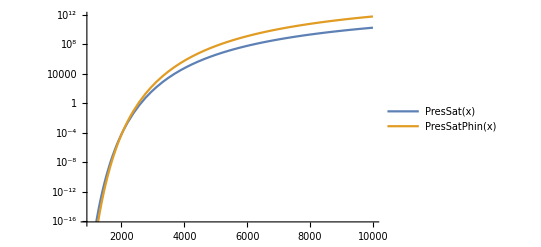

```mathematica
PresSat[T_]:=6 10^11 √T ⅇ^(-81200/T)

PresSatPhin[T_]:=6 10^15 ⅇ^(-92200/T)

PresGas[n_, T_] := n KB T

PresGas[10^6, 10000]
PresSat[10000]//N


LogPlot[{PresSat[x],PresSatPhin[x]}, {x,900, 10000}
,PlotLegends->"Expressions"]

Clear[T]
```

```mathematica
4/3 Pi 10^-15 2//N
```

8.37758×10^-15

```mathematica
ClearAll[Pvap,Pvap1,PresGas,f,md]




TimeSub[T_,n_]:=

Module[{a=0.1 10^-4,ρd=3.36,mmu=110,mDot,tEvap,mGrain,Pvap1},
mGrain = 4/3 Pi a^3 ρd;
Print["mGrain=", mGrain];

Pvap=n KB T;

Print["Pgas=", Pvap//N];

Pvap1=PresSatPhin[T];

Print["T=",T];
Print["PvapSat=",Pvap1//N];

mi=mmu*MP;

Print["mdot2=",
4Pi a^2*mi*√(2Pi KB T/mi) ];

mDot = 4Pi a^2 Pvap1 √(mi/(2Pi KB T));
Print["mDot=",mDot];


tEvap = mGrain/mDot;

Print["tEvap =",tEvap/DAY days ];


mDot

]



TimeSub[2000 , 0];

Clear[T]
```

mGrain=1.40743×10^-14

Pgas=0.

T=2000

PvapSat=0.000057171

mdot2=2.24519×10^-26

mDot=7.3985×10^-19

tEvap =0.220176 days

```mathematica
SubRate[T_]:= Subscript[P, vap] √(Subscript[m, a]/(2Pi KB T))//N
```

```mathematica
4Pi a^2 Pvap1 √(mi/(2Pi KB T))
```

S_i evaporation rate

```mathematica
f1[x_]:=Evaluate[ PadeApproximant[√x Exp[-A/x],{x,A,{1,1}}]]/.A->1 //N

f1[100]

(*Plot[(*f0[x]/.A->99990,*)
f[x],
{x,100,1000}
]*)
```

PadeApproximant[9.9005,{100.,1.,{1.,1.}}]

-Graphics-

```mathematica
ClearAll[f[x],A,T]
PadeApproximant[ⅇ^-T,{T,0,{1,1}}]]
```

```mathematica
PadeApproximant[Exp[x],{x,0,{2,3}}]
```

(1+(2 x)/5+x^2/20)/(1-(3 x)/5+(3 x^2)/20-x^3/60)

```mathematica
60*1.67
```

100.2

## Radiation penetration length

```mathematica
EddingtonLum[GM_, κ_]:=4Pi CL GM/κ;
EddingtonLum[Gr 10^7 Msol Subscript[M, 7], KPE]

RadSub[L_]:=Module[{Ts=1500},
	(L/(4Pi SGB Ts^4))^(1/2)]



Print["R_sub=",
RadSub[10^46 Subscript[L, 46]]/PC,"pc"]

Print["R_sub=",
RadSub[EddingtonLum[Gr 10^7 Msol Subscript[M, 7], KPE]]/PC,"pc"]
```

1.24949×10^45 M_7

R_sub=0.539619 √L_46pc

R_sub=0.190745 √M_7pc

```mathematica
(*X-ray opacity:*)
ClearAll[massGrnGrn,σUV,κUV,a,f]

massGrn[a_] := Module[{μm = 10^-4,ρd={3.36}},
		 4/3 Pi (a μm)^3 ρd]

σXR[E_] := If[E<0.5, 6 10^-23,
			If[E<7,2.6 10^-22,4.4 10^-22]]//N

σUV[a_]:= Module[{μm= 10^-4},
(a μm)^2]

κUV[a_]:= Module[{fd = 0.01 Subscript[f, 0.01]},
σUV[a]/massGrn[a]*fd
]

Print["κUV = ",
κUV[0.1 Subscript[a, 0.1]]
]

σUV[0.1 Subscript[a, 0.1]]
κUV[0.1 Subscript[a, 0.1]]
```

κUV = {(71.0513 f_0.01)/(a_0.1)}

1.×10^-10 a_0.1^2

{(71.0513 f_0.01)/(a_0.1)}

Dust to gas mass ratio
fd=0.01 Z

```mathematica
Print["κ_dust_UV=",
      Module[{μm = 10^-4},
(0.1μm)^2/10^-14*0.01 Subscript[f, 0.01]
]
]
```

κ_dust_UV=100. f_0.01

UV and X - ray penetration length, don’t forget that σ and κ are in cm^2 and cm^2/g!

```mathematica
ClearAll[dxl,dxl,LenPenetr,LenPenetrUV]

LenPenetrUV[n_] := Module[{ ad=0.1 Subscript[a, 0.1]},
 1/(κUV[ad] MP n)
]

LenPenetr[n_, σ_] := Module[{l=0},
 l=1/(σ n);
l]

σUV[0.1 Subscript[a, 0.1]]

σUV[0.1 Subscript[a, 0.1]]/SGT

Print["l_UV=",LenPenetrUV[10^5 Subscript[n, 5]]/RadSub[10^46 Subscript[L, 46]],"Rsub"
]

LenPenetr[10^5 Subscript[n, 5], {σXR[2],σXR[8]}]/RadSub[10^46 Subscript[L, 46]]

LenPenetr[10^5 Subscript[n, 5], SGT]/PC
```

1.×10^-10 a_0.1^2

1.50322×10^14 a_0.1^2

l_UV={(0.0505338 a_0.1)/(f_0.01 √L_46 n_5)}Rsub

{0.0230988/(√L_46 n_5),0.0136493/(√L_46 n_5)}

4.87159/n_5

```mathematica
RadFluxPres[T_, κ] := Module[{l=0},
 SGB T^4;
l]
```

1.24949×10^45

## Density from equal radiation and gas pressures

```mathematica
RhoPgasEqPrad[Tsub_]:=
Print["n [from Pgas = P rad ] = ",
	ARAD Tsub^3/(RGAS MP), 
"\n ",
"P_rad=" , ARAD Tsub^4]

RhoPgasEqPrad[1500 Subscript[T, 1500]]
```

n [from Pgas = P rad ] = 1.83676×10^11 T_1500^3
 P_rad=0.038296 T_1500^4

```mathematica
Pi(0.1 10^-4)^2
```

3.14159×10^-10

q - parameter
q=R_sub/r_(disk,sub)

```mathematica
ClearAll[L]
qParam = ((f Ledd)/(4 π σ T^4))^(1/2)(3/(8π))((G M Md)/(σ T^4))^(-1/3)
qParam = qParam /.Ledd->(4π c G M)/κT

qParam = FullSimplify[qParam,L>0 &&f>0 && σ>0 && c>0 && G>0 &&Md>0 && M>0&&T>0 && κT>0] 

%/.{f->0.1, κT->KPE, c->CL, G->Gr,M->MBH, σ->SGB, T->1500,Md->0.1MsolYr}
```

(3 √((f Ledd)/(T^4 σ)))/(16 π^(3/2) ((G M Md)/(T^4 σ))^(1/3))

(3 √((c f G M)/(T^4 κT σ)))/(8 π ((G M Md)/(T^4 σ))^(1/3))

(3 √((c f)/κT) ((G M)/σ)^(1/6))/(8 π (Md T^2)^(1/3))

0.721872

Viscous time - scale

Visouc time-scale :
t_v=1/(α Ω_K)(r/H)^2

```mathematica
Vtherm[T_]:= Module[{μ=1},(RGAS/μ T)^(1/2)]
OmegaOrb[r_,M_]:=√(Gr M) r^(-3/2)

VelocOrb[r_,M_]:=√(Gr M) r^(-1/2)
```

Dynamical time - scale

```mathematica
rs = SchwarzchildRadius[MBH]


tDynam[r_, α_] :=Module[{Ω},

OmegaOrb[r]
Print["t_dyn = 1/Ω =  ",1/Ω/YR, "yr \n",
1/Ω, "s"]

] 

(*tDynam[0.01PC Subscript[r, -2], 0.1 Subscript[α, 0.1]]*)

tDynam[1600 rs, 0.1 Subscript[α, 0.1]]

tDynam[10^4 rs, 0.1 Subscript[α, 0.1]]

tDynam[10^-1 PC, 0.1 Subscript[α, 0.1]]
```

```mathematica
1/OmegaOrb[10^-1 PC Subscript[r, 0.1],MBH]/YR
```

149.224 r_0.1^(3/2)

```mathematica
tTherm[r_, α_] :=Module[{Ω},

Ω=OmegaOrb[r,MBH];

Print["t_th = 1/(α Ω) =  ",1/(α Ω)/YR, "yr"]
] 

tTherm[10^-1 PC Subscript[r, -1],0.1 Subscript[α, 0.1]]
```

t_th = 1/(α Ω) =  (1492.24 r_-1^(3/2))/(α_0.1)yr

```mathematica
ClearAll[T, tVisc]

tVisc[r_,α_, T_] :=Module[{Ω,h2r},
Ω=OmegaOrb[r,MBH];
h2r = Vtherm[T]/VelocOrb[r, MBH] ;
Print["t_vis = r/v_r =  ",1/(α Ω)h2r^-2/YR, "yr"]
] 


tVisc[10^-1 PC Subscript[r, -1], 0.1 Subscript[α, 0.1], 1500 Subscript[T, 1500]]
```

t_vis = r/v_r =  (5.14703×10^7 √(r_-1))/(T_1500 α_0.1)yr

```mathematica
Rin

tVisc[Rin,0.1 Subscript[α, 0.1]]
```

1.66337×10^16 ((M_7^2 η_0.5)/(ϵ_0.1))^(1/3)

t_vis = r/v_r =  (3.58507×10^8 ((M_7^2 η_0.5)/(ϵ_0.1))^(1/6))/(T_50 α_0.1)yr

```mathematica
Print["λ_m = ",

2 Pi Vtherm[T]/OmegaOrb[r,M]/.{ r->10^-2 PC Subscript[r, -2], M->Subscript[M, 7] 10^7 Msol, T->1400 Subscript[T, 1400]}

]
```

λ_m = (3.18926×10^14 r_-2^(3/2) √T_1400)/(√M_7)

```mathematica
B=((Gr MBH 10^-2 MsolYr)/(8 Pi SGB 1500^4(0.5PC)^3))^(1/4);
A=10^2;




ClearAll[A,B]
```

0.0133312

100

Disk radiation flux angular dependence
d (θ) = cos (θ) (1 + 2cos (θ))

```mathematica
KPUV=100;
η = 0.1;
dTheta = Cos[t](1+2Cos[t])/.Cos[t]->x;

A = KPE/KPUV 1/η;

roots =Solve[dTheta-A==0 && x>0, x]

Eq  = Cos[t]-x/.roots[[1]]

Solve[
Eq==0,t
]

Pi/2//N
```

```mathematica
90-1.5335595898124028/Pi*180
```

2.13351

(* Eddington Mdot *)

```mathematica
EddingtonLum[GM_, κ_]:=4Pi CL GM/κ;

EddingtonLum[Gr MBH Subscript[M, 7], KPE]/CL^2/MsolYr/(0.057 Subscript[ϵ, sch])
```

(0.386711 M_7)/ϵ_sch

```mathematica
Radial radiation force in the disk:
```

```mathematica
0.1 MsolYr/(MP 10^10(0.001PC)^2 CL)
```

0.00132099

Virial Temperature :

Based on the enthalpy argument: Virial Temperature:
T_v=T_(v,g)(5+8 P_r/P_g)^-1, where T_vir=(G M)/(ρ r).

ρ W_g=γ/(γ-1)P_g+4 P_r,  where gravitational energy: W_g=GM/(2r)

```mathematica
ClearAll[n,r,Subscript[W, g],ρ,γ,rul]
Subscript[W, g]=.
TvirImplicitEq=-ρ Subscript[W, g]+(0* γ)/(γ-1)Subscript[P, g]+4 Subscript[P, r]/.{Subscript[P, r]-> a T^4/3,Subscript[P, g]->ρ Rg T/μ}
TvirImplicitCoefList = CoefficientList[TvirImplicitEq,T]

γ=5/3;

n=10^11;

r=0.01PC;


Subscript[W, g]=(Gr MBH)/(2r);

rul={ρ->n MP, Rg->RGAS,μ->1,a->ARAD};

Print@"ρ W_g ="  
TvirImplicitCoefList[[1]]/.rul

"(Rg γ ρ)/((-1 + γ) μ)="
TvirImplicitCoefList[[2]]/.rul

"(4 a)/3="
TvirImplicitCoefList[[5]]/.rul


TvirImplicitEq=TvirImplicitEq/.rul

Solve[TvirImplicitEq==0 && T>0,T,Reals]
```

ClearAll::ssym: W_g is not a symbol or a string.

Unset::norep: Assignment on Subscript for W_g not found.

$Failed

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of T_50.

Hold[TvirImplicitEq=-ρ W_g+((0 γ) P_g)/(γ-1)+4 P_r/.{P_r→(a T^4)/3,P_g→(ρ Rg T)/μ}]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of T_50.

Hold[TvirImplicitCoefList=CoefficientList[TvirImplicitEq,T]]

ρ W_g =

Part::partd: Part specification TvirImplicitCoefList⟦1⟧ is longer than depth of object.

TvirImplicitCoefList⟦1⟧

(Rg γ ρ)/((-1 + γ) μ)=

Part::partd: Part specification TvirImplicitCoefList⟦2⟧ is longer than depth of object.

TvirImplicitCoefList⟦2⟧

(4 a)/3=

Part::partd: Part specification TvirImplicitCoefList⟦5⟧ is longer than depth of object.

TvirImplicitCoefList⟦5⟧

TvirImplicitEq

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of T_50.

Hold[Solve[TvirImplicitEq==0&&T>0,T,ℝ]]

-35.9574+0.0000347495 T+1.00862×10^-14 T^4

```mathematica
Subscript[T, v][n_, r_,M_]:=Module[{G=Gr,Subscript[P, r]=ARAD T^4/3, Subscript[P, g]},
(G M)/(n MP r)(5+8 Subscript[P, r]/Subscript[P, g])^-1
]
```

# Hydrogen partial ionization 6000 K, and Iron bump T=1.8 10^5

```mathematica
RadHydrogenIoniz[M_, Mdot_,T_]:=(Gr^(1/3) M^(1/3) (3/Pi)^(1/3) Mdot^(1/3))/(2 SGB^(1/3) T^(4/3))

r0 = RadHydrogenIoniz[MBH, 0.01MsolYr,6000]
rFe = RadHydrogenIoniz[MBH, 0.01MsolYr,1.8 10^5]

((Gr MBH)/r0)^(1/2)/10^5

((Gr MBH)/rFe)^(1/2)/10^5
```

1.10774×10^15

1.18835×10^13

10943.6

105659.

6.30708×10^24